```mathematica
energy=Λ+1/Λ(1+ArcSin[Ξ(1-d)/(l02 Λ)]^2/(2Ξ^2))
```

Λ+(1+ArcSin[((1-d) Ξ)/(l02 Λ)]^2/(2 Ξ^2))/Λ

```mathematica
Series[energy/.l02->a Ξ,{Ξ,Infinity,4}]
```

(1/Λ+Λ)+ArcSin[(1-d)/(a Λ)]^2/(2 Λ Ξ^2)+O[1/Ξ]^5

```mathematica
Simplify[Series[(1+Λ^2)/Λ-(Log[-(4 (-1+d)^2 Ξ^2)/(l02^2 Λ^2)]^2)/(8 Λ Ξ^2)+(l02^2 Λ Log[-(4 (-1+d)^2 Ξ^2)/(l02^2 Λ^2)])/(8 (-1+d)^2 Ξ^4)/.{Λ->1+λ},{λ,0,4}]]
```

(2+(l02^2 Log[-(4 (-1+d)^2 Ξ^2)/l02^2])/(8 (-1+d)^2 Ξ^4)-(Log[-(4 (-1+d)^2 Ξ^2)/l02^2]^2)/(8 Ξ^2))+((-(2 l02^2)/(-1+d)^2+(l02^2/(-1+d)^2+4 Ξ^2) Log[-(4 (-1+d)^2 Ξ^2)/l02^2]+Ξ^2 Log[-(4 (-1+d)^2 Ξ^2)/l02^2]^2) λ)/(8 Ξ^4)+1/8 (8-l02^2/((-1+d)^2 Ξ^4)-(4+6 Log[-(4 (-1+d)^2 Ξ^2)/l02^2]+Log[-(4 (-1+d)^2 Ξ^2)/l02^2]^2)/Ξ^2) λ^2+(-1+l02^2/(24 (-1+d)^2 Ξ^4)+(8+22/3 Log[-(4 (-1+d)^2 Ξ^2)/l02^2]+Log[-(4 (-1+d)^2 Ξ^2)/l02^2]^2)/(8 Ξ^2)) λ^3+(1-l02^2/(48 (-1+d)^2 Ξ^4)-(35+25 Log[-(4 (-1+d)^2 Ξ^2)/l02^2]+3 Log[-(4 (-1+d)^2 Ξ^2)/l02^2]^2)/(24 Ξ^2)) λ^4+O[λ]^5

```mathematica
D[energy,Λ]
```

1-((1-d) ArcSin[((1-d) Ξ)/(l02 Λ)])/(l02 Λ^3 Ξ √(1-((1-d)^2 Ξ^2)/(l02^2 Λ^2)))-(1+ArcSin[((1-d) Ξ)/(l02 Λ)]^2/(2 Ξ^2))/Λ^2

```mathematica
Clear[d,l02,Ξ]
```

```mathematica
d=0.2;Ξ=10;l02=1;
```

```mathematica
Plot[energy,{Λ,0,1}]
```

-Graphics-

```mathematica
Simplify[D[energy,{Λ,2}]]
```

-((2 (-1+d)^2 Λ)/(-l02^2 Λ^2+(-1+d)^2 Ξ^2)+(2 (-1+d)^3 Ξ ArcSin[(Ξ-d Ξ)/(l02 Λ)])/(l02^3 Λ^2 (1-((-1+d)^2 Ξ^2)/(l02^2 Λ^2))^(3/2))+(8 (-1+d) ArcSin[(Ξ-d Ξ)/(l02 Λ)])/(l02 Ξ √(1-((-1+d)^2 Ξ^2)/(l02^2 Λ^2)))-2 Λ (2+ArcSin[(Ξ-d Ξ)/(l02 Λ)]^2/Ξ^2))/(2 Λ^4)

```mathematica
1-((1-d) ArcSin[((1-d) Ξ)/(l02 Λ)])/(l02 Λ^3 Ξ √(1-((1-d)^2 Ξ^2)/(l02^2 Λ^2)))-(1+ArcSin[((1-d) Ξ)/(l02 Λ)]^2/(2 Ξ^2))/Λ^2/.{Ξ->1/ξ}
```

1-((1-d) ξ ArcSin[(1-d)/(l02 Λ ξ)])/(l02 Λ^3 √(1-(1-d)^2/(l02^2 Λ^2 ξ^2)))-(1+1/2 ξ^2 ArcSin[(1-d)/(l02 Λ ξ)]^2)/Λ^2

```mathematica
-((2 (-1+d)^2 Λ)/(-l02^2 Λ^2+(-1+d)^2 Ξ^2)+(2 (-1+d)^3 Ξ ArcSin[(Ξ-d Ξ)/(l02 Λ)])/(l02^3 Λ^2 (1-((-1+d)^2 Ξ^2)/(l02^2 Λ^2))^(3/2))+(8 (-1+d) ArcSin[(Ξ-d Ξ)/(l02 Λ)])/(l02 Ξ √(1-((-1+d)^2 Ξ^2)/(l02^2 Λ^2)))-2 Λ (2+ArcSin[(Ξ-d Ξ)/(l02 Λ)]^2/Ξ^2))/(2 Λ^4)/.{Ξ->1/ξ}
```

-((2 (-1+d)^2 Λ)/(-l02^2 Λ^2+(-1+d)^2/ξ^2)+(2 (-1+d)^3 ArcSin[(1/ξ-d/ξ)/(l02 Λ)])/(l02^3 Λ^2 (1-(-1+d)^2/(l02^2 Λ^2 ξ^2))^(3/2) ξ)+(8 (-1+d) ξ ArcSin[(1/ξ-d/ξ)/(l02 Λ)])/(l02 √(1-(-1+d)^2/(l02^2 Λ^2 ξ^2)))-2 Λ (2+ξ^2 ArcSin[(1/ξ-d/ξ)/(l02 Λ)]^2))/(2 Λ^4)

```mathematica
l02 Λ Ψ^3/(16Ξ^3)+Ψ^2/(24Λ Ξ^2)-l02 Λ Ψ/(2Ξ)+1/Λ/.{Ξ->1/ξ}
```

1/Λ-1/2 l02 Λ ξ Ψ+(ξ^2 Ψ^2)/(24 Λ)+1/16 l02 Λ ξ^3 Ψ^3

```mathematica
Ξ(1-d)-l02 Λ Sin[Ψ/2]/.{Ξ->1/ξ}
```

(1-d)/ξ-l02 Λ Sin[Ψ/2]

```mathematica
{1-((1-d) ξ ArcSin[(1-d)/(l02 Λ ξ)])/(l02 Λ^3 √(1-(1-d)^2/(l02^2 Λ^2 ξ^2)))-(1+1/2 ξ^2 ArcSin[(1-d)/(l02 Λ ξ)]^2)/Λ^2,1/Λ-1/2 l02 Λ ξ Ψ+(ξ^2 Ψ^2)/(24 Λ)+1/16 l02 Λ ξ^3 Ψ^3,(1-d)/ξ-l02 Λ Sin[Ψ/2],-((2 (-1+d)^2 Λ)/(-l02^2 Λ^2+(-1+d)^2/ξ^2)+(2 (-1+d)^3 ArcSin[(1/ξ-d/ξ)/(l02 Λ)])/(l02^3 Λ^2 (1-(-1+d)^2/(l02^2 Λ^2 ξ^2))^(3/2) ξ)+(8 (-1+d) ξ ArcSin[(1/ξ-d/ξ)/(l02 Λ)])/(l02 √(1-(-1+d)^2/(l02^2 Λ^2 ξ^2)))-2 Λ (2+ξ^2 ArcSin[(1/ξ-d/ξ)/(l02 Λ)]^2))/(2 Λ^4)}/.{l02->lm1/ξ+l0+l1 ξ+O[ξ]^2,Ψ->Ψ0+Ψ1 ξ+O[ξ]^2,Λ->1+Λ1 ξ+Λ2 ξ^2+O[ξ]^3}
```

{2 Λ1 ξ+(1/2 (-6 Λ1^2+4 Λ2)-((1-d) ArcSin[(1-d)/lm1])/(lm1 √((-1+2 d-d^2+lm1^2)/lm1^2))-1/2 ArcSin[(1-d)/lm1]^2) ξ^2+O[ξ]^3,(1-(lm1 Ψ0)/2)+(-Λ1+1/2 (-l0 Ψ0-lm1 (Λ1 Ψ0+Ψ1))) ξ+O[ξ]^2,(1-d-lm1 Sin[Ψ0/2])/ξ+(-l0 Sin[Ψ0/2]-lm1 (1/2 Ψ1 Cos[Ψ0/2]+Λ1 Sin[Ψ0/2]))+O[ξ]^1,2-6 Λ1 ξ+1/2 (-(2 (-1+d)^2)/((-1+d)^2-lm1^2)-16 Λ1^2+2 (20 Λ1^2-8 Λ2)-(2 (-1+d)^3 ArcSin[(1-d)/lm1])/(lm1^3 ((-1+2 d-d^2+lm1^2)/lm1^2)^(3/2))-(8 (-1+d) ArcSin[(1-d)/lm1])/(lm1 √((-1+2 d-d^2+lm1^2)/lm1^2))+2 (2 Λ2+ArcSin[(1-d)/lm1]^2)) ξ^2+O[ξ]^3}

```mathematica
Solve[2 Λ1==0&&1-(lm1 Ψ0)/2==0&& 1-d-lm1 Sin[Ψ0/2]==0,{Λ1,lm1,Ψ0}]
```

$Aborted

```mathematica
{1-((1-d) ξ^2 ArcSin[(1-d)/(l02 Λ)])/(l02 √(1-(1-d)^2/(l02^2 Λ^2)) Λ^3)-(1+1/2 ξ^2 ArcSin[(1-d)/(l02 Λ)]^2)/Λ^2,1/Λ-1/2 l02 Λ ξ Ψ+(ξ^2 Ψ^2)/(24 Λ)+1/16 l02 Λ ξ^3 Ψ^3,(1-d)/ξ-l02 Λ Sin[Ψ/2]}//.{lm1->2/Ψ0,l02->lm1/ξ+l0+l1 ξ+O[ξ]^2,Ψ->Ψ0+Ψ1 ξ+O[ξ]^2,Λ->1+Λ2 ξ^2+O[ξ]^3}
```

{2 Λ2 ξ^2+O[ξ]^3,1/2 (-l0 Ψ0-(2 Ψ1)/Ψ0) ξ+O[ξ]^2,(1-d-(2 Sin[Ψ0/2])/Ψ0)/ξ+(-(Ψ1 Cos[Ψ0/2])/Ψ0-l0 Sin[Ψ0/2])+O[ξ]^1}

```mathematica
Solve[1/2 (-l0 Ψ0-(2 Ψ1)/Ψ0) ==0&&(-(Ψ1 Cos[Ψ0/2])/Ψ0-l0 Sin[Ψ0/2])==0,{l0,Ψ1}]
```

{{l0→0,Ψ1→0}}

```mathematica
{1-((1-d) ξ^2 ArcSin[(1-d)/(l02 Λ)])/(l02 √(1-(1-d)^2/(l02^2 Λ^2)) Λ^3)-(1+1/2 ξ^2 ArcSin[(1-d)/(l02 Λ)]^2)/Λ^2,1/Λ-1/2 l02 Λ ξ Ψ+(ξ^2 Ψ^2)/(24 Λ)+1/16 l02 Λ ξ^3 Ψ^3,(1-d)/ξ-l02 Λ Sin[Ψ/2]}//.{lm1->2/Ψ0,l02->lm1/ξ+l1 ξ+O[ξ]^2,Ψ->Ψ0+Ψ2 ξ^2+O[ξ]^3,Λ->1+Λ3 ξ^3+O[ξ]^4}
```

{2 Λ3 ξ^3+O[ξ]^4,(Ψ0^2/6+1/2 (-l1 Ψ0-(2 Ψ2)/Ψ0)) ξ^2+O[ξ]^3,(1-d-(2 Sin[Ψ0/2])/Ψ0)/ξ+(-(Ψ2 Cos[Ψ0/2])/Ψ0-l1 Sin[Ψ0/2]) ξ+O[ξ]^2}

```mathematica
Solve[Ψ0^2/6+1/2 (-l1 Ψ0-(2 Ψ2)/Ψ0)==0&&(-(Ψ2 Cos[Ψ0/2])/Ψ0-l1 Sin[Ψ0/2])==0,{l1,Ψ2}]
```

{{l1→(Ψ0^2 Cos[Ψ0/2])/(3 (Ψ0 Cos[Ψ0/2]-2 Sin[Ψ0/2])),Ψ2→-(Ψ0^3 Sin[Ψ0/2])/(3 (Ψ0 Cos[Ψ0/2]-2 Sin[Ψ0/2]))}}

```mathematica
Simplify[{1-((1-d) ξ^2 ArcSin[(1-d)/(l02 Λ)])/(l02 √(1-(1-d)^2/(l02^2 Λ^2)) Λ^3)-(1+1/2 ξ^2 ArcSin[(1-d)/(l02 Λ)]^2)/Λ^2,1/Λ-1/2 l02 Λ ξ Ψ+(ξ^2 Ψ^2)/(24 Λ)+1/16 l02 Λ ξ^3 Ψ^3,(1-d)/ξ-l02 Λ Sin[Ψ/2]}//.{lm1->2/Ψ0,l1->(Ψ0^2 Cos[Ψ0/2])/(3 (Ψ0 Cos[Ψ0/2]-2 Sin[Ψ0/2])),Ψ2->-(Ψ0^3 Sin[Ψ0/2])/(3 (Ψ0 Cos[Ψ0/2]-2 Sin[Ψ0/2])),l02->lm1/ξ+l1 ξ+O[ξ]^2,Ψ->Ψ0+Ψ2 ξ^2+O[ξ]^3,Λ->1+Λ4 ξ^4+O[ξ]^5}]
```

{(2 Λ4-3/8 (-1+d)^2 Ψ0^2) ξ^4+O[ξ]^5,O[ξ]^3,(1-d-(2 Sin[Ψ0/2])/Ψ0)/ξ+O[ξ]^2}

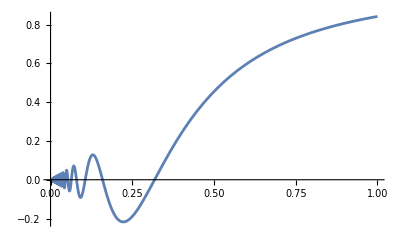

```mathematica
Plot[x Sin[1/x],{x,0,1}]
```